# Music Genre Classifier

## Loading the Dataset.

```mathematica
rockdata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/rock/*.au"];
rockdata1=Flatten[AudioSplit[#,15]&/@rockdata];
countrydata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/country/*.au"];
```

```mathematica
countrydata1=Flatten[AudioSplit[#,15]&/@countrydata];
```

```mathematica
bluesdata =Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/blues/*.au"];
bluesdata1=Flatten[AudioSplit[#,15]&/@bluesdata];
```

```mathematica
classicaldata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/classical/*.au"];
```

```mathematica
classicaldata1=Flatten[AudioSplit[#,15]&/@classicaldata];
```

```mathematica
discodata =Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/disco/*.au"];
```

```mathematica
discodata1=Flatten[AudioSplit[#,15]&/@discodata];
```

```mathematica
Length@discodata1
```

200

```mathematica
hiphopdata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/hiphop/*.au"];
```

```mathematica
hiphopdata1=Flatten[AudioSplit[#,15]&/@hiphopdata];
```

```mathematica
jazzdata =Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/jazz/*.au"];
jazzdata1=Flatten[AudioSplit[#,15]&/@jazzdata];
```

```mathematica
metaldata =Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/metal/*.au"];
metaldata1=Flatten[AudioSplit[#,15]&/@metaldata];
```

```mathematica
popdata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/pop/*.au"];
```

```mathematica
popdata1=Flatten[AudioSplit[#,15]&/@popdata];
```

```mathematica
reggaedata = Import["/Users/aishwaryapraveen/Desktop/Summer School Project/genres/reggae/*.au"];
```

```mathematica
reggaedata1 = Flatten[AudioSplit[#,15]&/@reggaedata];
```

Extracting MFCC Values

```mathematica
mFCCFeaturesreggaedata=(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@reggaedata1;
mFCCFeaturesClassReggae=Thread[mFCCFeaturesreggaedata->"reggae"];
```

```mathematica
mFCCFeaturespopdata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@popdata1;
mFCCFeaturesClassPop =Thread[mFCCFeaturespopdata->"pop"];
```

```mathematica
mFCCFeaturesmetaldata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@metaldata1;
mFCCFeaturesClassMetal = Thread[mFCCFeaturesmetaldata->"metal"];
```

```mathematica
mFCCFeaturesjazzdata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@jazzdata1;
mFCCFeaturesClassJazz =Thread[mFCCFeaturesjazzdata ->"jazz"];
```

```mathematica
mFCCFeatureshiphopdata = (Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@hiphopdata1;
mFCCFeaturesClasshiphop = Thread[mFCCFeatureshiphopdata->"hiphop"];
```

```mathematica
mFCCFeaturesdiscodata = (Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@discodata1;
mFCCFeaturesClassdisco = Thread[mFCCFeaturesdiscodata -> "disco"];
```

```mathematica
mFCCFeaturesbluesdata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@bluesdata1;
mFCCFeaturesClassblues = Thread[mFCCFeaturesbluesdata ->"blues"];
```

```mathematica
mFCCFeaturesclassicaldata = (Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@classicaldata1;
mFCCFeaturesClassclassical =Thread[mFCCFeaturesclassicaldata->"classical"];
```

```mathematica
mFCCFeaturesrockdata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@rockdata1;
mFCCFeaturesClassrock = Thread[mFCCFeaturesrockdata->"rock"];
```

```mathematica
mFCCFeaturescountrydata =(Values@AudioLocalMeasurements[#,"MFCC",PartitionGranularity->{1.,1.}])&/@countrydata1;
mFCCFeaturesClasscountry = Thread[mFCCFeaturescountrydata ->"country"];
```

## Using Neural Networks

First, We will test a RNN on just three genres of our dataset.

```mathematica
net=NetChain[{
GatedRecurrentLayer[128],
GatedRecurrentLayer[128],
SequenceLastLayer[],
LinearLayer[],
SoftmaxLayer[]},
"Input"-> {"Varying",13},
"Output"->NetDecoder[{"Class",{"metal","pop","reggae"}}]]
```

NetChain[]

```mathematica
data= RandomSample[Join[mFCCFeaturesClassPop,mFCCFeaturesClassReggae,mFCCFeaturesClassMetal]];
```

```mathematica
trainSet1=data[[1;;540]];
validationSet1=data[[541;;]];
```

```mathematica
trainedNet=NetTrain[net,trainSet1,ValidationSet->validationSet1,MaxTrainingRounds->100]
```

NetChain[]

```mathematica
cl5= ClassifierMeasurements[trainedNet,validationSet1]
```

ClassifierMeasurementsObject[…]

```mathematica
cl5["Accuracy"]
```

0.733333

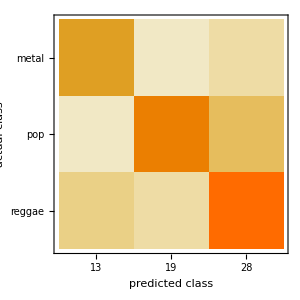

```mathematica
cl5["ConfusionMatrixPlot"]
```

We will apply a different version of the above network to all the genres.

```mathematica
net4=NetChain[{
GatedRecurrentLayer[256],
GatedRecurrentLayer[256],
GatedRecurrentLayer[256],
SequenceLastLayer[],
LinearLayer[],
SoftmaxLayer[]},
"Input"-> {"Varying",13},
"Output"->NetDecoder[{"Class",{"country","blues","disco","hiphop","jazz","metal","pop","reggae","rock","classical"}}]
]
```

NetChain[]

```mathematica
data= RandomSample[Join[mFCCFeaturesClassPop,mFCCFeaturesClassReggae,mFCCFeaturesClassMetal,mFCCFeaturesClassJazz,mFCCFeaturesClassblues,mFCCFeaturesClassclassical,mFCCFeaturesClasscountry,mFCCFeaturesClassdisco,mFCCFeaturesClassrock,mFCCFeaturesClasshiphop]];
```

```mathematica
trainSet=data[[1;;1900]];
validationSet=data[[1901;;]];
```

```mathematica
trainednet4=NetTrain[net4,trainSet,ValidationSet->validationSet,MaxTrainingRounds->100]
```

NetChain[]

```mathematica
cl4= ClassifierMeasurements[trainednet4,validationSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cl4["Accuracy"]
```

0.75

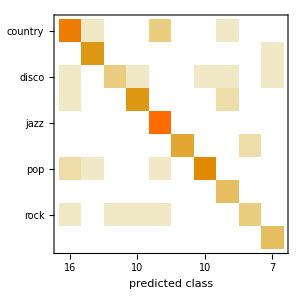

```mathematica
cl4["ConfusionMatrixPlot"]
```

```mathematica
findGenre[sound_]:=With[{audio=Values@AudioLocalMeasurements[AudioResample[sound,22050],"MFCC",PartitionGranularity->{1.,1.}]},
trainednet4[audio]
]
```

```mathematica
findGenre[rockdata[[-3]]]
```

rock

## Inbuilt Classifier

The inbuilt Classifier is using the logistic regression method to classify the songs. With just an accuracy of 39 %, the classifer performs poorly on the testing set.

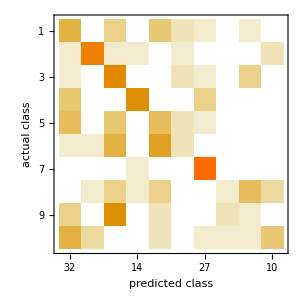
```mathematica
ClassifierInformation[c]

{{"Classifier information"}, {{{"Method", "Logistic regression"}, {"Number of classes", 10}, {"Number of features", 1}, {"Number of training examples", 1800}, {"L1 regularization coefficient", 0}, {"L2 regularization coefficient", 1000.}}}}
cm=ClassifierMeasurements[c,Testingdata]
ClassifierMeasurementsObject[…]
cm["Accuracy"]
0.39
-Graphics-
```